```mathematica
β[ω_,δ_,t_,ϵ_]:=β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[12],Join[Table[{i,i-1},{i,Range[2,12,1]}],Table[{i,i+1},{i,Range[1,12,1]}]]->-t]
```

```mathematica
T[t_]:=T[t]=t*IdentityMatrix[12]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.001,1,0]],A:=Inverse[β[ω,0.001,1,0]],T:=T[1]},Do[J=Inverse[IdentityMatrix[12]-A.T.J.T].A,13200];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[12]-g[ω,δ,t,ϵ].T[1].LEFT[ω,δ,t,ϵ].T[1]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[12]-g[ω,δ,t,ϵ].T[1].LEFT[ω,δ,t,ϵ].T[1]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[12]-SL[ω,0.001,1,0].T[1].SR[ω,0.001,1,0].T[1]].SL[ω,0.001,1,0]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].SL[ω,0.001,1,0].T[1]].SR[ω,0.001,1,0]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,0.001,1,0].T[1].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T[1].grr[ω,δ,t,ϵ].T[1]-T[1].GNON[ω,δ,t,ϵ].T[1].GNON[ω,δ,t,ϵ]]
```

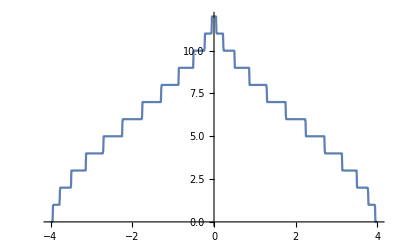
{774.911,-Graphics-}

```mathematica
Timing[ListLinePlot[Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[-4,4,0.01]}]]]
```

```mathematica
imp[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{gg=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,12}]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
υ[ϵ1_,τ_]:=Module[{μ1=RandomInteger[{1,12}],μ2=RandomInteger[{1,12}],μ3=RandomInteger[{1,12}],μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}],μ6=RandomInteger[{1,12}],μ7=RandomInteger[{1,12}],μ8=RandomInteger[{1,12}]},
(*Print[{μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8}];*)
η5:=Module[{gg=g[ω,0.001,1,0],T=1*IdentityMatrix[12],imp=imp[ω,0.001,1,0,ϵ1],m=RandomInteger[{0,1}],n=RandomInteger[{0,1}],o=RandomInteger[{0,1}],p=RandomInteger[{0,1}],q=RandomInteger[{0,1}]},(*Print[{m+n+o+p+q+4}];*)sl1= Module[{J=SL[ω,0.001,1,0]},Do[J=Inverse[IdentityMatrix[12]-gg.T.J.T].gg,n]; J=J];sl2=Inverse[IdentityMatrix[12]-imp.T.sl1.T].imp; sl3=Module[{J=sl2},Do[J=Inverse[IdentityMatrix[12]-gg.T.J.T].gg,m]; J=J];sl4=Inverse[IdentityMatrix[12]-imp.T.sl3.T].imp; sl5=Module[{J=sl4},Do[J=Inverse[IdentityMatrix[12]-gg.T.J.T].gg,o]; J=J];sl6=Inverse[IdentityMatrix[12]-imp.T.sl5.T].imp; sl7=Module[{J=sl6},Do[J=Inverse[IdentityMatrix[12]-gg.T.J.T].gg,p]; J=J];sl8=Inverse[IdentityMatrix[12]-imp.T.sl7.T].imp; sl9=Module[{J=sl8},Do[J=Inverse[IdentityMatrix[12]-gg.T.J.T].gg,q]; J=J];Il1:=Inverse[IdentityMatrix[12]-sl9.T.SR[ω,0.001,1,0].T].sl9;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T.sl9.T].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T.Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
Clear[m5];m5:=m5=Table[{ω,η5},{ω,Range[0,4,0.01]}];ρ2:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/12sq/2imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/12sq/3imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/12sq/4imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/12sq/5imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/12sq/6imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ7:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/12sq/7imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ8:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/12sq/8imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];(*
ρ9:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/12sq/9imp/9imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ10:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/12sq/10imp/10imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)]*);
list:={{2,ρ2},{3,ρ3},{4,ρ4},{5,ρ5},{6,ρ6},{7,ρ7},{8,ρ8}(*{9,ρ9},{10,ρ10}*)};Print[list];{list[[Position[list,Min[list]][[1,1]],1]],Min[list]}]
```

```mathematica
Timing[υ[0.3,3.99]]
```

{{2,0.00157879},{3,0.00146165},{4,0.00184545},{5,0.0026274},{6,0.00228816},{7,0.00221136},{8,0.00249639}}

{2.89488,{3,0.00146165}}

```mathematica
Clear[f]
```

```mathematica
f[τ_]:=f[τ]=Table[υ[0.3,τ],50]
```

```mathematica
ϕ[τ_]:=2*(Count[Part[f[τ],;;,1],6]+Count[Part[f[τ],;;,1],7]+Count[Part[f[τ],;;,1],8])/100
```

```mathematica
Timing[f[3.99]]
```

{{2,0.00135064},{3,0.00141639},{4,0.00188002},{5,0.00370026},{6,0.00268353},{7,0.00204528},{8,0.00213983}}

{{2,0.00352997},{3,0.00369482},{4,0.00427879},{5,0.00677899},{6,0.00516654},{7,0.00411349},{8,0.00424732}}

{{2,0.00706325},{3,0.00754307},{4,0.0081977},{5,0.0110377},{6,0.00916977},{7,0.00788719},{8,0.00797609}}

{{2,0.00136177},{3,0.0012366},{4,0.00164849},{5,0.00266631},{6,0.00255171},{7,0.00249675},{8,0.00260597}}

{{2,0.00059567},{3,0.000901746},{4,0.00151054},{5,0.00362483},{6,0.00269741},{7,0.00209359},{8,0.00207458}}

{{2,0.00368587},{3,0.00397538},{4,0.0041649},{5,0.00726782},{6,0.00594505},{7,0.00538525},{8,0.00541774}}

{{2,0.01094},{3,0.0105568},{4,0.010361},{5,0.00947119},{6,0.0092274},{7,0.0104201},{8,0.0126159}}

{{2,0.00210004},{3,0.0021622},{4,0.00253135},{5,0.00307089},{6,0.00261359},{7,0.00266413},{8,0.00350171}}

{{2,0.0113627},{3,0.00969363},{4,0.00855915},{5,0.00490983},{6,0.00594545},{7,0.00832315},{8,0.011508}}

{{2,0.00607314},{3,0.00662037},{4,0.00726273},{5,0.00859316},{6,0.00669157},{7,0.00593005},{8,0.00704351}}

{{2,0.00784542},{3,0.0063656},{4,0.00527492},{5,0.00284443},{6,0.00485848},{7,0.00757579},{8,0.00951141}}

{{2,0.00359192},{3,0.0036964},{4,0.00411207},{5,0.00610639},{6,0.00485548},{7,0.00409299},{8,0.00429536}}

{{2,0.0050836},{3,0.00552326},{4,0.00636818},{5,0.00700573},{6,0.00598487},{7,0.0055325},{8,0.00621508}}

{{2,0.00153605},{3,0.00126696},{4,0.00136616},{5,0.00193392},{6,0.00156642},{7,0.00167951},{8,0.00231789}}

{{2,0.00303844},{3,0.00343768},{4,0.00401149},{5,0.00646737},{6,0.00478853},{7,0.00391879},{8,0.00440481}}

{{2,0.00907014},{3,0.00829274},{4,0.00762737},{5,0.00729081},{6,0.00618433},{7,0.0070202},{8,0.00982653}}

{{2,0.00217199},{3,0.00266457},{4,0.00345156},{5,0.00568366},{6,0.00515559},{7,0.00444977},{8,0.00377871}}

{{2,0.00620113},{3,0.00656405},{4,0.00741861},{5,0.00876572},{6,0.00680392},{7,0.00548225},{8,0.00653124}}

{{2,0.0134539},{3,0.0140131},{4,0.0151051},{5,0.0153107},{6,0.0126582},{7,0.0109431},{8,0.0123978}}

{{2,0.00285435},{3,0.00275024},{4,0.00280414},{5,0.00424473},{6,0.00297219},{7,0.00259781},{8,0.00359316}}

{{2,0.00363794},{3,0.00342953},{4,0.00352696},{5,0.00495788},{6,0.0036852},{7,0.00345658},{8,0.0047072}}

{{2,0.0044051},{3,0.00444084},{4,0.00473939},{5,0.00662261},{6,0.00523824},{7,0.00454538},{8,0.00508281}}

{{2,0.0118678},{3,0.01056},{4,0.00975392},{5,0.00659467},{6,0.00664705},{7,0.00838568},{8,0.0120332}}

{{2,0.00100048},{3,0.00120827},{4,0.0015841},{5,0.00338964},{6,0.00246445},{7,0.00199172},{8,0.00238888}}

{{2,0.00565045},{3,0.00544301},{4,0.00581772},{5,0.00573162},{6,0.005465},{7,0.00551848},{8,0.00602151}}

{{2,0.0083434},{3,0.00866304},{4,0.00911216},{5,0.0103092},{6,0.00787753},{7,0.00717193},{8,0.00913696}}

{{2,0.0241125},{3,0.0218553},{4,0.0207075},{5,0.0143418},{6,0.0178091},{7,0.0219009},{8,0.0253112}}

{{2,0.00476457},{3,0.00560106},{4,0.00681177},{5,0.0085682},{6,0.00646921},{7,0.00500058},{8,0.00550537}}

{{2,0.00337814},{3,0.00313941},{4,0.00326184},{5,0.00385035},{6,0.00329718},{7,0.00350444},{8,0.00463032}}

{{2,0.0036837},{3,0.00281042},{4,0.00234471},{5,0.00134559},{6,0.00198025},{7,0.00331633},{8,0.00472507}}

{{2,0.00197298},{3,0.00288715},{4,0.00396903},{5,0.00784677},{6,0.0060087},{7,0.00411668},{8,0.00298056}}

{{2,0.0233259},{3,0.0207246},{4,0.0192925},{5,0.0128532},{6,0.0164562},{7,0.0207975},{8,0.0246127}}

{{2,0.00173029},{3,0.00160257},{4,0.00170754},{5,0.00347438},{6,0.00265758},{7,0.00251288},{8,0.00305265}}

{{2,0.000521102},{3,0.000630109},{4,0.00108224},{5,0.00290711},{6,0.0020467},{7,0.00147824},{8,0.00158766}}

{{2,0.0018796},{3,0.00139361},{4,0.00120915},{5,0.00216805},{6,0.00231412},{7,0.00280116},{8,0.0032676}}

{{2,0.00417413},{3,0.00308332},{4,0.00261569},{5,0.00161441},{6,0.00239647},{7,0.0037276},{8,0.00497295}}

{{2,0.00467309},{3,0.00495358},{4,0.00565283},{5,0.00629969},{6,0.0055206},{7,0.00526412},{8,0.00595297}}

{{2,0.0189431},{3,0.0181502},{4,0.0181226},{5,0.0140021},{6,0.0152348},{7,0.017262},{8,0.0197417}}

{{2,0.00446036},{3,0.00376416},{4,0.00367578},{5,0.00286074},{6,0.00342873},{7,0.00425312},{8,0.00514732}}

{{2,0.00325422},{3,0.00272594},{4,0.00269148},{5,0.00246326},{6,0.0022041},{7,0.00275667},{8,0.00431892}}

{{2,0.0248264},{3,0.0221813},{4,0.0203788},{5,0.0138303},{6,0.0178065},{7,0.0226595},{8,0.0263142}}

{{2,0.0136155},{3,0.0148261},{4,0.0161006},{5,0.0174439},{6,0.0156893},{7,0.0148881},{8,0.0155981}}

{{2,0.00718406},{3,0.00737236},{4,0.00806069},{5,0.0088274},{6,0.00802972},{7,0.00747798},{8,0.00786368}}

{{2,0.00656586},{3,0.0052691},{4,0.00413717},{5,0.00262998},{6,0.00345954},{7,0.00548145},{8,0.00763084}}

{{2,0.00501968},{3,0.00509868},{4,0.00538622},{5,0.00570793},{6,0.00568747},{7,0.00619767},{8,0.00687131}}

{{2,0.00422306},{3,0.00380106},{4,0.00367544},{5,0.00451813},{6,0.00430743},{7,0.00470045},{8,0.00525154}}

{{2,0.00446247},{3,0.00440766},{4,0.00477641},{5,0.0054902},{6,0.00509661},{7,0.00497365},{8,0.00526204}}

{{2,0.000628056},{3,0.000811347},{4,0.00126865},{5,0.00290919},{6,0.0021723},{7,0.00171249},{8,0.00181368}}

{{2,0.00975473},{3,0.00917008},{4,0.00932817},{5,0.00765568},{6,0.00734829},{7,0.00786483},{8,0.0101635}}

{{2,0.00697167},{3,0.00584058},{4,0.00523771},{5,0.00290407},{6,0.00386088},{7,0.0057115},{8,0.00809402}}

{133.25,{{2,0.00135064},{2,0.00352997},{2,0.00706325},{3,0.0012366},{2,0.00059567},{2,0.00368587},{6,0.0092274},{2,0.00210004},{5,0.00490983},{7,0.00593005},{5,0.00284443},{2,0.00359192},{2,0.0050836},{3,0.00126696},{2,0.00303844},{6,0.00618433},{2,0.00217199},{7,0.00548225},{7,0.0109431},{7,0.00259781},{3,0.00342953},{2,0.0044051},{5,0.00659467},{2,0.00100048},{3,0.00544301},{7,0.00717193},{5,0.0143418},{2,0.00476457},{3,0.00313941},{5,0.00134559},{2,0.00197298},{5,0.0128532},{3,0.00160257},{2,0.000521102},{4,0.00120915},{5,0.00161441},{2,0.00467309},{5,0.0140021},{5,0.00286074},{6,0.0022041},{5,0.0138303},{2,0.0136155},{2,0.00718406},{5,0.00262998},{2,0.00501968},{4,0.00367544},{3,0.00440766},{2,0.000628056},{6,0.00734829},{5,0.00290407}}}

```mathematica
Last[%117]
```

{{2,0.00135064},{2,0.00352997},{2,0.00706325},{3,0.0012366},{2,0.00059567},{2,0.00368587},{6,0.0092274},{2,0.00210004},{5,0.00490983},{7,0.00593005},{5,0.00284443},{2,0.00359192},{2,0.0050836},{3,0.00126696},{2,0.00303844},{6,0.00618433},{2,0.00217199},{7,0.00548225},{7,0.0109431},{7,0.00259781},{3,0.00342953},{2,0.0044051},{5,0.00659467},{2,0.00100048},{3,0.00544301},{7,0.00717193},{5,0.0143418},{2,0.00476457},{3,0.00313941},{5,0.00134559},{2,0.00197298},{5,0.0128532},{3,0.00160257},{2,0.000521102},{4,0.00120915},{5,0.00161441},{2,0.00467309},{5,0.0140021},{5,0.00286074},{6,0.0022041},{5,0.0138303},{2,0.0136155},{2,0.00718406},{5,0.00262998},{2,0.00501968},{4,0.00367544},{3,0.00440766},{2,0.000628056},{6,0.00734829},{5,0.00290407}}

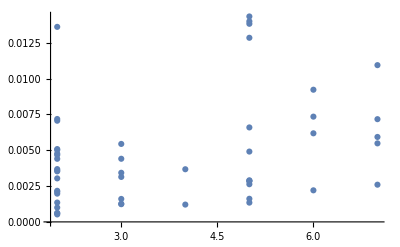

```mathematica
ListPlot[%118]
```

```mathematica
Last[%104]
```

{{6,0.0023765},{5,0.00296876},{2,0.00105413},{4,0.00303608},{4,0.00177399},{2,0.00321575},{2,0.00487456},{7,0.012091},{7,0.00435671},{4,0.00271182},{4,0.00269921},{3,0.00117512},{7,0.00357132},{6,0.00300432},{5,0.00296049},{2,0.00104099},{6,0.00254331},{6,0.00230317},{4,0.00146255},{5,0.00249346},{2,0.00170014},{5,0.014042},{3,0.000738616},{4,0.00293751},{6,0.00201432},{3,0.00142671},{6,0.00255927},{7,0.00789149},{6,0.00317713},{2,0.00386983},{2,0.00277375},{5,0.00250934},{3,0.000767926},{3,0.00202722},{2,0.000837202},{2,0.00210405},{5,0.0108356},{6,0.00241428},{7,0.00797233},{2,0.000986348},{5,0.00184088},{3,0.00209646},{7,0.00238119},{4,0.00166151},{2,0.00355619},{5,0.00153494},{3,0.00164215},{5,0.00252872},{5,0.00998738},{3,0.00127812}}

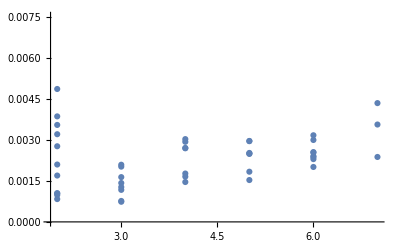

```mathematica
ListPlot[%105]
```

```mathematica
Last[%94]
```

{{4,0.00108389},{2,0.00285395},{3,0.000494982},{3,0.00115337},{3,0.000544623},{5,0.00440732},{3,0.000491469},{4,0.00123947},{2,0.000697387},{2,0.00115218},{4,0.000662553},{5,0.00169042},{5,0.00186307},{5,0.00129107},{2,0.000685741},{5,0.00156874},{4,0.000421477},{4,0.00071331},{5,0.00242368},{5,0.00239931},{5,0.00448213},{5,0.00375763},{5,0.0014052},{5,0.00202277},{4,0.000658676},{5,0.00631032},{5,0.00335024},{5,0.00607169},{5,0.00063117},{2,0.00155506},{4,0.000911331},{2,0.000671634},{5,0.00469394},{5,0.00286715},{4,0.000551627},{5,0.000856709},{4,0.000689406},{5,0.000842016},{4,0.00150452},{4,0.000968526},{5,0.000607937},{3,0.00142441},{5,0.00436744},{5,0.000767856},{5,0.00176065},{4,0.000794818},{5,0.00104025},{5,0.0052787},{3,0.000409022},{5,0.0105863}}

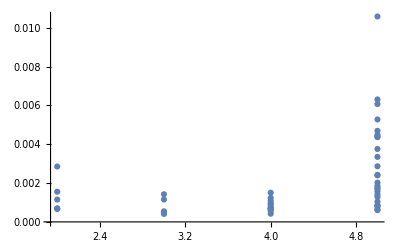

```mathematica
ListPlot[%95]
```

```mathematica
Table[{τ,ϕ[τ]},{τ,Range[0.1,3.99,0.1]}]
```

```mathematica
Table[{τ,ϕ[τ]},{τ,Range[0.1,3.99,0.1]}]
```

{{0.1,17/50},{0.2,9/25},{0.3,1/2},{0.4,23/50},{0.5,9/25},{0.6,1/2},{0.7,3/5},{0.8,13/25},{0.9,27/50},{1.,29/50},{1.1,14/25},{1.2,3/5},{1.3,17/25},{1.4,17/25},{1.5,17/25},{1.6,31/50},{1.7,14/25},{1.8,14/25},{1.9,16/25},{2.,14/25},{2.1,16/25},{2.2,31/50},{2.3,31/50},{2.4,14/25},{2.5,31/50},{2.6,29/50},{2.7,16/25},{2.8,33/50},{2.9,29/50},{3.,3/5},{3.1,17/25},{3.2,31/50},{3.3,4/5},{3.4,29/50},{3.5,7/10},{3.6,7/10},{3.7,13/25},{3.8,18/25},{3.9,29/50}}

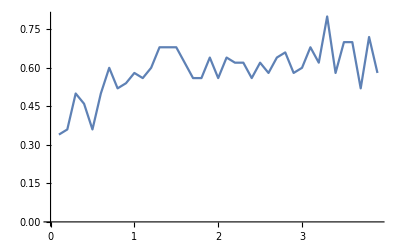

```mathematica
ListPlot[%27,Joined->True]
```

{5,8,6,6}

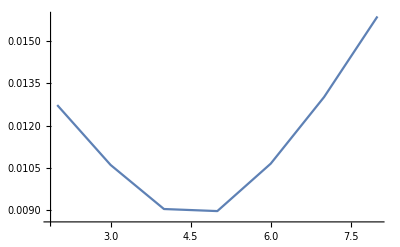

{{2,0.012733},{3,0.0106107},{4,0.00904782},{5,0.00897482},{6,0.0106557},{7,0.0130173},{8,0.0158734}}

```mathematica
(*μ1=RandomInteger[{1,12}]; μ2=RandomInteger[{1,12}]; μ3=RandomInteger[{1,12}]; μ4=RandomInteger[{1,12}]; μ5=RandomInteger[{1,12}]; μ6=RandomInteger[{1,12}]; μ7=RandomInteger[{1,12}]; μ8=RandomInteger[{1,12}];
Print[{μ1(*,μ2*),μ3(*,μ4*),μ5(*,μ6,μ7*),μ8}]
Clear[m5]
test[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[12]-imp1.T[1].SL[ω,0.001,1,0].T[1]].imp1;
Sl12:=Inverse[IdentityMatrix[12]-imp2.T[1].Sl11.T[1]].imp2;
Sl13:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl12.T[1]].imp3;
Sl14:=Inverse[IdentityMatrix[12]-imp4.T[1].Sl13.T[1]].imp4;
Sl15:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl14.T[1]].imp3;
Sl16:=Inverse[IdentityMatrix[12]-imp6.T[1].Sl15.T[1]].imp6;
Sl17:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl16.T[1]].imp3;
Sl18:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl17.T[1]].imp3;
Il1:=Inverse[IdentityMatrix[12]-Sl18.T[1].SR[ω,0.001,1,0].T[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].Sl18.T[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
m5[ϵ1_]:=m5[ϵ1]=Table[{ω,test[ω,0.001,1,0,ϵ1]},{ω,Range[0,4,0.01]}]
ρ2[ϵ1_]:=Module[{B1=Transpose[{m5[ϵ1][[1;;400]][[;;,1]],(m5[ϵ1][[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/12sq/2imp6.csv"][[1;;400,;;]][[;;,2]])^2}]}, Integrate[Interpolation[B1][ω],{ω,0,3.99}]/400]
ρ3[ϵ1_]:=Module[{B1=Transpose[{m5[ϵ1][[1;;400]][[;;,1]],(m5[ϵ1][[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/12sq/3imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,3.99}]/400]
ρ4[ϵ1_]:=Module[{B1=Transpose[{m5[ϵ1][[1;;400]][[;;,1]],(m5[ϵ1][[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/12sq/4imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,3.99}]/400]
ρ5[ϵ1_]:=Module[{B1=Transpose[{m5[ϵ1][[1;;400]][[;;,1]],(m5[ϵ1][[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/12sq/5imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,3.99}]/400]
ρ6[ϵ1_]:=Module[{B1=Transpose[{m5[ϵ1][[1;;400]][[;;,1]],(m5[ϵ1][[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/12sq/6imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,3.99}]/400]
ρ7[ϵ1_]:=Module[{B1=Transpose[{m5[ϵ1][[1;;400]][[;;,1]],(m5[ϵ1][[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/12sq/7imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,3.99}]/400]
ρ8[ϵ1_]:=Module[{B1=Transpose[{m5[ϵ1][[1;;400]][[;;,1]],(m5[ϵ1][[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/12sq/8imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,3.99}]/400]
A9[ϵ1_]:={{2,ρ2[ϵ1]},{3,ρ3[ϵ1]},{4,ρ4[ϵ1]},{5,ρ5[ϵ1]},{6,ρ6[ϵ1]},{7,ρ7[ϵ1]},{8,ρ8[ϵ1]}}
ListLinePlot[A9[0.6]]
(*Show[ListLinePlot[m5[0.6]],ListLinePlot[Import["/home/shardulmukim/PhD/fwi/12sq/8imp6.csv"],PlotStyle->Red](*,ListLinePlot[Import["/home/shardulmukim/PhD/fwi/12sq/4imp/4imp6.csv"],PlotStyle->Brown](*,ListLinePlot[Import["/home/shardulmukim/PhD/fwi/12sq/4imp/4imp6.csv"],PlotStyle->Red]*),ListLinePlot[Import["/home/shardulmukim/PhD/fwi/12sq/6imp/6imp6.csv"],PlotStyle->Green]*)]*)
A9[0.6]*)
```

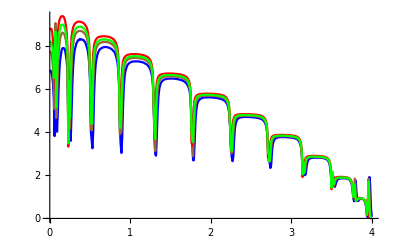

```mathematica
(*Show[(*ListLinePlot[m5[0.6]],*)ListLinePlot[Import["/home/shardulmukim/PhD/fwi/12sq/8imp6.csv"],PlotStyle->Blue],ListLinePlot[Import["/home/shardulmukim/PhD/fwi/12sq/6imp6.csv"],PlotStyle->Brown],ListLinePlot[Import["/home/shardulmukim/PhD/fwi/12sq/4imp6.csv"],PlotStyle->Red],ListLinePlot[Import["/home/shardulmukim/PhD/fwi/12sq/5imp6.csv"],PlotStyle->Green],PlotRange->All]
*)
```